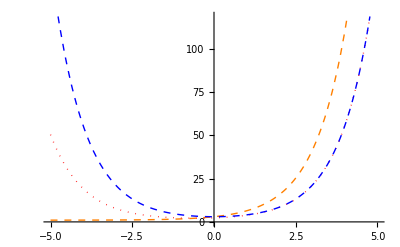

```mathematica
<<PlotLegends`;
Plot[{Exp[x]+Exp[x]+1,1+Exp[x]+1/(2+1)*Exp[-x],1+Exp[x]+Exp[-x]},{x,-5,5},PlotStyle->{{Orange,Dashed,Thick},{Red,Dotted,Thick},{Blue,Dashed}},PlotLegend->{"Part 1+2","Part 3","Part 4"},LegendPosition->{1.1,-0.4}]
```

```mathematica
Integrate[Exp[-a t]DiracDelta[t-t0],t]
Integrate[Exp[-a t]HeavisideTheta[t-t0],t]
```

ⅇ^(-a t0) HeavisideTheta[t-t0]

((-ⅇ^(-a t)+ⅇ^(-a t0)) HeavisideTheta[t-t0])/a

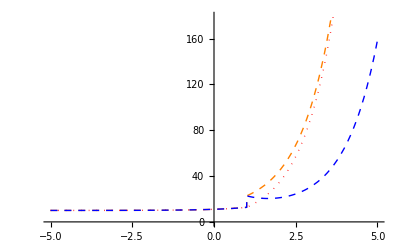

```mathematica
D0=1;
g=1;
c=1;
I0=10;
t0=1;
El=10;
τ=0.001;
U1[t_] = D0 Exp[g/c t]+ I0/g Exp[g/c(t-t0)]HeavisideTheta[t-t0]+El;
U2[t_] = D0 Exp[g/c t]+ I0/g  HeavisideTheta[t-t0] (Exp[g/c(t-t0)]-1)+El;
U3[t_] = D0 Exp[g/c t] +I0/g *1/(τ/c+1)*HeavisideTheta[t-t0]*(Exp[-g/c*(t-t0)])+El;
<<PlotLegends`;
Plot[{U1[t],U2[t],U3[t]},{t,-5,5},PlotStyle->{{Orange,Dashed,Thick},{Red,Dotted,Thick},{Blue,Dashed}},PlotLegend->{"Part 1","Part 2","Part 3"},LegendPosition->{1.1,-0.4}]
```